```mathematica
Quit[]
```

### Coordinate TFs for n=6

```mathematica
CartToSpher={Table[x[ii]->r[ii] Cos[ϕ[ii]]Sin[θ[ii]],{ii,1,6}],Table[y[ii]->r[ii] Sin[ϕ[ii]]Sin[θ[ii]],{ii,1,6}],Table[z[ii]->r[ii] Cos[θ[ii]],{ii,1,6}]}//Flatten;
SpherToCart={Table[r[ii]->Sqrt[x[ii]^2+y[ii]^2+z[ii]^2],{ii,1,6}],Table[ϕ[ii]->ArcTan[Sqrt[x[ii]^2+y[ii]^2]/z[ii]],{ii,1,6}],Table[θ[ii]->ArcTan[y[ii]/x[ii]],{ii,1,6}]}//Flatten;
SpherToCartij={Table[Table[r[ii,jj]->Sqrt[(x[ii]-x[jj])^2+(y[ii]-y[jj])^2+(z[ii]-z[jj])^2],{ii,1,6}],{jj,1,6}],Table[Table[ϕ[ii,jj]->ArcTan[Sqrt[(x[ii]-x[jj])^2+(y[ii]-y[jj])^2]/(z[ii]-z[jj])],{ii,1,6}],{jj,1,6}],Table[Table[θ[ii,jj]->ArcTan[y[ii]-y[jj]/x[ii]-x[jj]],{ii,1,6}],{jj,1,6}]}//Flatten;
```

### Potential and WF

```mathematica
(*6-quark potential, where B=(-Subscript[C, F])/(N-1)Subscript[α, s]?*)
```

```mathematica
V[r[i,j]]=B*Sum[If[jj>ii,1/r[ii,jj],0],{ii,1,6},{jj,1,6}]
```

B (1/(r(1,3))+1/(r(1,4))+1/(r(1,5))+1/(r(1,6))+1/(r(2,3))+1/(r(2,4))+1/(r(2,5))+1/(r(2,6))+1/(r(3,4))+1/(r(3,5))+1/(r(3,6))+1/(r(4,5))+1/(r(4,6))+1/(r(5,6))+1/(r(1,2)))

```mathematica
(*Total 6-quark WF*)
```

```mathematica
Ψ[r[i]]=1/6!SumPerms ψ[r[1],r[2],r[3],r[4],r[5],r[6]]
```

1/720 SumPerms ψ(r(1),r(2),r(3),r(4),r(5),r(6))

```mathematica
ψ[r[i]]=1/6!SumPerms χ[r[1]]χ[r[2]]χ[r[3]]χ[r[4]]χ[r[5]]χ[r[6]]
```

1/720 SumPerms χ(r(1)) χ(r(2)) χ(r(3)) χ(r(4)) χ(r(5)) χ(r(6))

```mathematica
χ[r[i]]=Sum[HWF[i,jj,a,b,c],{jj,1,6}]/6
```

1/6 (HWF(i,1,a,b,c)+HWF(i,2,a,b,c)+HWF(i,3,a,b,c)+HWF(i,4,a,b,c)+HWF(i,5,a,b,c)+HWF(i,6,a,b,c))

### Defining HWFs and their Laplacians

```mathematica
(*Hydrogen WFs in spherical rij TFd to ri and rj*)
```

```mathematica
(* a0 tunable in our case *)
```

```mathematica
HWF[i_,j_,a_,b_,c_]:=ResourceFunction["HydrogenWavefunction"][{a,b,c},a0,{r[i,j],θ[i,j],ϕ[i,j]}];
```

```mathematica
(* TF from rij to ri and rj*)
```

```mathematica
HWFTF[i_,j_,a_,b_,c_]:=HWF[i,j,a,b,c]/.SpherToCartij/.CartToSpher//Simplify
```

```mathematica
(* for example .. *)
```

```mathematica
HWFTF[1,2,1,0,0]
```

(√(1/a0^3) exp(-(√(-2 r(2) r(1) sin(θ(1)) sin(θ(2)) sin(ϕ(1)) sin(ϕ(2))-2 r(2) r(1) sin(θ(1)) sin(θ(2)) cos(ϕ(1)) cos(ϕ(2))-2 r(2) r(1) cos(θ(1)) cos(θ(2))+(r(1))^2+(r(2))^2))/a0))/(√π)

```mathematica
(* or .. *)
```

```mathematica
(* Spherical Laplacian *)
```

```mathematica
LaplaceSpher[f_,i_]:=Laplacian[f,{r[i],θ[i],ϕ[i]},"Spherical"];
```

```mathematica
(* for example .. *)
```

```mathematica
LaplaceSpher[HWFTF[1,2,1,0,0],1]//Expand//Simplify
```

(√(1/a0^3) (√(-2 r(2) r(1) sin(θ(1)) sin(θ(2)) sin(ϕ(1)) sin(ϕ(2))-2 r(2) r(1) sin(θ(1)) sin(θ(2)) cos(ϕ(1)) cos(ϕ(2))-2 r(2) r(1) cos(θ(1)) cos(θ(2))+(r(1))^2+(r(2))^2)-2 a0) exp(-1/a0(√(-2 r(2) r(1) sin(θ(1)) sin(θ(2)) sin(ϕ(1)) sin(ϕ(2))-2 r(2) r(1) sin(θ(1)) sin(θ(2)) cos(ϕ(1)) cos(ϕ(2))-2 r(2) r(1) cos(θ(1)) cos(θ(2))+(r(1))^2+(r(2))^2))))/(√π a0^2 √(-2 r(2) r(1) sin(θ(1)) sin(θ(2)) sin(ϕ(1)) sin(ϕ(2))-2 r(2) r(1) sin(θ(1)) sin(θ(2)) cos(ϕ(1)) cos(ϕ(2))-2 r(2) r(1) cos(θ(1)) cos(θ(2))+(r(1))^2+(r(2))^2))

```mathematica
((-1/2(LaplaceSpher[HWFTF[1,2,1,0,0]HWFTF[1,3,1,0,0]HWFTF[2,3,1,0,0],1])/.a0:>2/B//Expand)-(B (HWFTF[1,2,1,0,0]HWFTF[1,3,1,0,0]HWFTF[2,3,1,0,0]*(1/r[1,2]+1/r[2,3]+1/r[1,3])/.SpherToCartij/.CartToSpher/.a0:>2/B//Expand)//Expand))/(HWFTF[1,2,1,0,0]HWFTF[1,3,1,0,0]HWFTF[2,3,1,0,0])/.a0:>2/B/.r[1]:>1/.r[2]:>2/.r[3]:>3/.θ[__]:>0.5/.ϕ[__]:>0.3/.B:>1//Simplify//Expand
```

-2.25

```mathematica
B[N_,m_,nf_]:=Sqrt[(N+1)^2/(2N)^2/(11 N/3-2/3nf)^2 1/Log[m/.2]^2]
```

```mathematica
BQQ[N_,m_,nf_]:=Sqrt[((N^2-1)/(2N))^2/(11 N/3-2/3nf)^2 1/Log[m/.2]^2]
```

```mathematica
testB[[1,1]]^2*1.07/(BQQ[3,2*10^0,3]^2*.25)
```

1.07

```mathematica
testBQQ=Table[BQQ[3,2*10^xx,3]//N,{xx,0,5}]
```

{0.0643399,0.03217,0.0214466,0.016085,0.012868,0.0107233}

```mathematica
testBQQ^2*1/4
```

{0.00103491,0.000258727,0.00011499,0.0000646817,0.0000413963,0.0000287474}

```mathematica
testB=Table[Table[B[yy,2*10^xx,yy]//N,{xx,0,5}],{yy,3,6}]
```

(0.03217 | 0.016085 | 0.0107233 | 0.00804249 | 0.00643399 | 0.00536166
0.0226195 | 0.0113098 | 0.00753983 | 0.00565488 | 0.0045239 | 0.00376992
0.0173718 | 0.00868589 | 0.00579059 | 0.00434294 | 0.00347436 | 0.0028953
0.0140744 | 0.00703718 | 0.00469145 | 0.00351859 | 0.00281487 | 0.00234573)

```mathematica
TestB2=testB^2
```

(0.00103491 | 0.000258727 | 0.00011499 | 0.0000646817 | 0.0000413963 | 0.0000287474
0.000511642 | 0.00012791 | 0.0000568491 | 0.0000319776 | 0.0000204657 | 0.0000142123
0.000301779 | 0.0000754447 | 0.000033531 | 0.0000188612 | 0.0000120711 | 8.38274×10^-6
0.000198088 | 0.0000495219 | 0.0000220097 | 0.0000123805 | 7.9235×10^-6 | 5.50243×10^-6)

```mathematica
(TestB2[[2,4]]*2.79)/(TestB2[[1,4]]*1.07)
```

1.2891

```mathematica
testBQQ^2*1/4//StandardForm
```

{0.00103491,0.000258727,0.00011499,0.0000646817,0.0000413963,0.0000287474}

```mathematica
TestB2[[1]]*1.07
```

{0.00110735,0.000276837,0.000123039,0.0000692094,0.000044294,0.0000307597}

```mathematica
TestB2[[2]]*2.29
```

{0.00117166,0.000292915,0.000130184,0.0000732288,0.0000468664,0.0000325461}

```mathematica
TestB2[[3]]*5.7
```

{0.00172014,0.000430035,0.000191127,0.000107509,0.0000688055,0.0000477816}

```mathematica
TestB2[[4]]*10.2
```

{0.00202049,0.000505123,0.000224499,0.000126281,0.0000808197,0.0000561248}

### Taking Laplacian of sub-WFs

```mathematica
(*Total 6-quark WF*)
```

```mathematica
Ψ[r[i]]=1/6!SumPerms ψ[r[1],r[2],r[3],r[4],r[5],r[6]]
```

1/720 SumPerms ψ(r(1),r(2),r(3),r(4),r(5),r(6))

```mathematica
ψ[r[i]]=1/6!SumPerms χ[r[1]]χ[r[2]]χ[r[3]]χ[r[4]]χ[r[5]]χ[r[6]]
```

```mathematica
χ[i_,a_,b_,c_,n_]:=Sum[HWFTF[i,jj,a,b,c],{jj,1,n}]/n;
```

```mathematica
χ[1,1,0,0,6]
```

1/6 ((√(1/a0^3) exp(-(√(-2 r(2) r(1) sin(θ(1)) sin(θ(2)) sin(ϕ(1)) sin(ϕ(2))-2 r(2) r(1) sin(θ(1)) sin(θ(2)) cos(ϕ(1)) cos(ϕ(2))-2 r(2) r(1) cos(θ(1)) cos(θ(2))+(r(1))^2+(r(2))^2))/a0))/(√π)+(√(1/a0^3) exp(-(√(-2 r(3) r(1) sin(θ(1)) sin(θ(3)) sin(ϕ(1)) sin(ϕ(3))-2 r(3) r(1) sin(θ(1)) sin(θ(3)) cos(ϕ(1)) cos(ϕ(3))-2 r(3) r(1) cos(θ(1)) cos(θ(3))+(r(1))^2+(r(3))^2))/a0))/(√π)+(√(1/a0^3) exp(-(√(-2 r(4) r(1) sin(θ(1)) sin(θ(4)) sin(ϕ(1)) sin(ϕ(4))-2 r(4) r(1) sin(θ(1)) sin(θ(4)) cos(ϕ(1)) cos(ϕ(4))-2 r(4) r(1) cos(θ(1)) cos(θ(4))+(r(1))^2+(r(4))^2))/a0))/(√π)+(√(1/a0^3) exp(-(√(-2 r(5) r(1) sin(θ(1)) sin(θ(5)) sin(ϕ(1)) sin(ϕ(5))-2 r(5) r(1) sin(θ(1)) sin(θ(5)) cos(ϕ(1)) cos(ϕ(5))-2 r(5) r(1) cos(θ(1)) cos(θ(5))+(r(1))^2+(r(5))^2))/a0))/(√π)+(√(1/a0^3) exp(-(√(-2 r(6) r(1) sin(θ(1)) sin(θ(6)) sin(ϕ(1)) sin(ϕ(6))-2 r(6) r(1) sin(θ(1)) sin(θ(6)) cos(ϕ(1)) cos(ϕ(6))-2 r(6) r(1) cos(θ(1)) cos(θ(6))+(r(1))^2+(r(6))^2))/a0))/(√π)+(√(1/a0^3))/(√π))

## Wavefunction ansatz (test)

```mathematica
Clear[Psi]
```

```mathematica
For[n=1,n≤3,n++,
psi[n]=CC[n];
For[ii=1,ii≤3,ii++,For[jj=1,jj≤3,jj++,If[jj ≠ ii,If[jj>ii,psi[n]=psi[n]*Exp[-r[ii,jj]/a[n]/2],psi[n]=psi[n]*Exp[-r[jj,ii]/a[n]/2]]]]];]
```

```mathematica
(* n=2 *)
```

```mathematica
n=2;
```

```mathematica
psi=0;
For[ii=1,ii≤n,ii++,For[jj=ii,jj≤n,jj++,If[jj ≠ ii,If[jj>ii,psi=psi+Exp[-r[ii,jj]],psi=psi+Exp[-r[jj,ii]]]]]]
```

```mathematica
psi2=((psi^n//Expand)//.x__*Exp[y___]:>Exp[y]//ReplaceAll[#,z___*r[x___]:>r[x]]&)//.x__*Exp[y___]:>Exp[y]
```

ⅇ^(r(1,2))

```mathematica
psi3=psi2/.Exp[x___]:>C[Length[x//.r[a_,b_]:>r[a*b]]]Exp[x/a[Length[x//.r[a_,b_]:>r[a*b]]]]
```

1 ⅇ^((r(1,2))/(a(1)))

```mathematica
psi3//.{1. y_->y,E^x_->exp[x],r[x_,y_]:>rrSpher[x,y,r,t,p],a[x_]:>A[x]}//FortranForm
```

C(1)*exp(rrSpher(1,2,r,t,p)/A(1))

```mathematica
(* n=3 *)
```

```mathematica
n=3;
```

```mathematica
psi=0;
For[ii=1,ii≤n,ii++,For[jj=ii,jj≤n,jj++,If[jj ≠ ii,If[jj>ii,psi=psi+Exp[-r[ii,jj]],psi=psi+Exp[-r[jj,ii]]]]]]
```

```mathematica
psi2=((psi^n//Expand)//.x__*Exp[y___]:>Exp[y]//ReplaceAll[#,z___*r[x___]:>r[x]]&)//.x__*Exp[y___]:>Exp[y]
```

ⅇ^(r(1,2))+ⅇ^(r(1,3))+ⅇ^(r(1,2)+r(1,3))+ⅇ^(r(2,3))+ⅇ^(r(1,2)+r(2,3))+ⅇ^(r(1,3)+r(2,3))+ⅇ^(r(1,2)+r(1,3)+r(2,3))

```mathematica
psi3=psi2/.Exp[x___]:>C[Length[x//.r[a_,b_]:>r[a*b]]]Exp[x/a[Length[x//.r[a_,b_]:>r[a*b]]]]//Collect[#,C[___]]&
```

1 (ⅇ^((r(1,2))/(a(1)))+ⅇ^((r(1,3))/(a(1)))+ⅇ^((r(2,3))/(a(1))))+2 (ⅇ^((r(1,2)+r(1,3))/(a(2)))+ⅇ^((r(1,2)+r(2,3))/(a(2)))+ⅇ^((r(1,3)+r(2,3))/(a(2))))+3 ⅇ^((r(1,2)+r(1,3)+r(2,3))/(a(3)))

```mathematica
psi3//.{1. y_->y,E^x_->exp[x],r[x_,y_]:>rrSpher[x,y,r,t,p],a[x_]:>A[x]}//FortranForm
```

C(1)*(exp(rrSpher(1,2,r,t,p)/A(1)) + exp(rrSpher(1,3,r,t,p)/A(1)) + 
     -     exp(rrSpher(2,3,r,t,p)/A(1))) + 
     -  C(2)*(exp((rrSpher(1,2,r,t,p) + rrSpher(1,3,r,t,p))/A(2)) + 
     -     exp((rrSpher(1,2,r,t,p) + rrSpher(2,3,r,t,p))/A(2)) + 
     -     exp((rrSpher(1,3,r,t,p) + rrSpher(2,3,r,t,p))/A(2))) + 
     -  C(3)*exp((rrSpher(1,2,r,t,p) + rrSpher(1,3,r,t,p) + rrSpher(2,3,r,t,p))/A(3))

```mathematica
(* n=4 *)
```

```mathematica
n=4;
```

```mathematica
psi=0;
For[ii=1,ii≤n,ii++,For[jj=ii,jj≤n,jj++,If[jj ≠ ii,If[jj>ii,psi=psi+Exp[-r[ii,jj]],psi=psi+Exp[-r[jj,ii]]]]]]
```

```mathematica
psi2=((psi^n//Expand)//.x__*Exp[y___]:>Exp[y]//ReplaceAll[#,z___*r[x___]:>r[x]]&)//.x__*Exp[y___]:>Exp[y]
```

ⅇ^(r(1,2))+ⅇ^(r(1,3))+ⅇ^(r(1,2)+r(1,3))+ⅇ^(r(1,4))+ⅇ^(r(1,2)+r(1,4))+ⅇ^(r(1,3)+r(1,4))+ⅇ^(r(1,2)+r(1,3)+r(1,4))+ⅇ^(r(2,3))+ⅇ^(r(1,2)+r(2,3))+ⅇ^(r(1,3)+r(2,3))+ⅇ^(r(1,2)+r(1,3)+r(2,3))+ⅇ^(r(1,4)+r(2,3))+ⅇ^(r(1,2)+r(1,4)+r(2,3))+ⅇ^(r(1,3)+r(1,4)+r(2,3))+ⅇ^(r(1,2)+r(1,3)+r(1,4)+r(2,3))+ⅇ^(r(2,4))+ⅇ^(r(1,2)+r(2,4))+ⅇ^(r(1,3)+r(2,4))+ⅇ^(r(1,2)+r(1,3)+r(2,4))+ⅇ^(r(1,4)+r(2,4))+ⅇ^(r(1,2)+r(1,4)+r(2,4))+ⅇ^(r(1,3)+r(1,4)+r(2,4))+ⅇ^(r(1,2)+r(1,3)+r(1,4)+r(2,4))+ⅇ^(r(2,3)+r(2,4))+ⅇ^(r(1,2)+r(2,3)+r(2,4))+ⅇ^(r(1,3)+r(2,3)+r(2,4))+ⅇ^(r(1,2)+r(1,3)+r(2,3)+r(2,4))+ⅇ^(r(1,4)+r(2,3)+r(2,4))+ⅇ^(r(1,2)+r(1,4)+r(2,3)+r(2,4))+ⅇ^(r(1,3)+r(1,4)+r(2,3)+r(2,4))+ⅇ^(r(3,4))+ⅇ^(r(1,2)+r(3,4))+ⅇ^(r(1,3)+r(3,4))+ⅇ^(r(1,2)+r(1,3)+r(3,4))+ⅇ^(r(1,4)+r(3,4))+ⅇ^(r(1,2)+r(1,4)+r(3,4))+ⅇ^(r(1,3)+r(1,4)+r(3,4))+ⅇ^(r(1,2)+r(1,3)+r(1,4)+r(3,4))+ⅇ^(r(2,3)+r(3,4))+ⅇ^(r(1,2)+r(2,3)+r(3,4))+ⅇ^(r(1,3)+r(2,3)+r(3,4))+ⅇ^(r(1,2)+r(1,3)+r(2,3)+r(3,4))+ⅇ^(r(1,4)+r(2,3)+r(3,4))+ⅇ^(r(1,2)+r(1,4)+r(2,3)+r(3,4))+ⅇ^(r(1,3)+r(1,4)+r(2,3)+r(3,4))+ⅇ^(r(2,4)+r(3,4))+ⅇ^(r(1,2)+r(2,4)+r(3,4))+ⅇ^(r(1,3)+r(2,4)+r(3,4))+ⅇ^(r(1,2)+r(1,3)+r(2,4)+r(3,4))+ⅇ^(r(1,4)+r(2,4)+r(3,4))+ⅇ^(r(1,2)+r(1,4)+r(2,4)+r(3,4))+ⅇ^(r(1,3)+r(1,4)+r(2,4)+r(3,4))+ⅇ^(r(2,3)+r(2,4)+r(3,4))+ⅇ^(r(1,2)+r(2,3)+r(2,4)+r(3,4))+ⅇ^(r(1,3)+r(2,3)+r(2,4)+r(3,4))+ⅇ^(r(1,4)+r(2,3)+r(2,4)+r(3,4))

```mathematica
psi3=(psi2/.Exp[x___]:>C[Length[x//.r[a_,b_]:>r[a*b]]]Exp[x/a[Length[x//.r[a_,b_]:>r[a*b]]]])//Collect[#,C[___]]&
```

(ⅇ^((r(1,2))/(a(1)))+ⅇ^((r(1,3))/(a(1)))+ⅇ^((r(1,4))/(a(1)))+ⅇ^((r(2,3))/(a(1)))+ⅇ^((r(2,4))/(a(1)))+ⅇ^((r(3,4))/(a(1)))) 1+(ⅇ^((r(1,2)+r(1,3))/(a(2)))+ⅇ^((r(1,2)+r(1,4))/(a(2)))+ⅇ^((r(1,3)+r(1,4))/(a(2)))+ⅇ^((r(1,2)+r(2,3))/(a(2)))+ⅇ^((r(1,3)+r(2,3))/(a(2)))+ⅇ^((r(1,4)+r(2,3))/(a(2)))+ⅇ^((r(1,2)+r(2,4))/(a(2)))+ⅇ^((r(1,3)+r(2,4))/(a(2)))+ⅇ^((r(1,4)+r(2,4))/(a(2)))+ⅇ^((r(2,3)+r(2,4))/(a(2)))+ⅇ^((r(1,2)+r(3,4))/(a(2)))+ⅇ^((r(1,3)+r(3,4))/(a(2)))+ⅇ^((r(1,4)+r(3,4))/(a(2)))+ⅇ^((r(2,3)+r(3,4))/(a(2)))+ⅇ^((r(2,4)+r(3,4))/(a(2)))) 2+(ⅇ^((r(1,2)+r(1,3)+r(1,4))/(a(3)))+ⅇ^((r(1,2)+r(1,3)+r(2,3))/(a(3)))+ⅇ^((r(1,2)+r(1,4)+r(2,3))/(a(3)))+ⅇ^((r(1,3)+r(1,4)+r(2,3))/(a(3)))+ⅇ^((r(1,2)+r(1,3)+r(2,4))/(a(3)))+ⅇ^((r(1,2)+r(1,4)+r(2,4))/(a(3)))+ⅇ^((r(1,3)+r(1,4)+r(2,4))/(a(3)))+ⅇ^((r(1,2)+r(2,3)+r(2,4))/(a(3)))+ⅇ^((r(1,3)+r(2,3)+r(2,4))/(a(3)))+ⅇ^((r(1,4)+r(2,3)+r(2,4))/(a(3)))+ⅇ^((r(1,2)+r(1,3)+r(3,4))/(a(3)))+ⅇ^((r(1,2)+r(1,4)+r(3,4))/(a(3)))+ⅇ^((r(1,3)+r(1,4)+r(3,4))/(a(3)))+ⅇ^((r(1,2)+r(2,3)+r(3,4))/(a(3)))+ⅇ^((r(1,3)+r(2,3)+r(3,4))/(a(3)))+ⅇ^((r(1,4)+r(2,3)+r(3,4))/(a(3)))+ⅇ^((r(1,2)+r(2,4)+r(3,4))/(a(3)))+ⅇ^((r(1,3)+r(2,4)+r(3,4))/(a(3)))+ⅇ^((r(1,4)+r(2,4)+r(3,4))/(a(3)))+ⅇ^((r(2,3)+r(2,4)+r(3,4))/(a(3)))) 3+(ⅇ^((r(1,2)+r(1,3)+r(1,4)+r(2,3))/(a(4)))+ⅇ^((r(1,2)+r(1,3)+r(1,4)+r(2,4))/(a(4)))+ⅇ^((r(1,2)+r(1,3)+r(2,3)+r(2,4))/(a(4)))+ⅇ^((r(1,2)+r(1,4)+r(2,3)+r(2,4))/(a(4)))+ⅇ^((r(1,3)+r(1,4)+r(2,3)+r(2,4))/(a(4)))+ⅇ^((r(1,2)+r(1,3)+r(1,4)+r(3,4))/(a(4)))+ⅇ^((r(1,2)+r(1,3)+r(2,3)+r(3,4))/(a(4)))+ⅇ^((r(1,2)+r(1,4)+r(2,3)+r(3,4))/(a(4)))+ⅇ^((r(1,3)+r(1,4)+r(2,3)+r(3,4))/(a(4)))+ⅇ^((r(1,2)+r(1,3)+r(2,4)+r(3,4))/(a(4)))+ⅇ^((r(1,2)+r(1,4)+r(2,4)+r(3,4))/(a(4)))+ⅇ^((r(1,3)+r(1,4)+r(2,4)+r(3,4))/(a(4)))+ⅇ^((r(1,2)+r(2,3)+r(2,4)+r(3,4))/(a(4)))+ⅇ^((r(1,3)+r(2,3)+r(2,4)+r(3,4))/(a(4)))+ⅇ^((r(1,4)+r(2,3)+r(2,4)+r(3,4))/(a(4)))) 4

```mathematica
psi3//.{1. y_->y,E^x_->exp[x],r[x_,y_]:>rrSpher[x,y,r,t,p],a[x_]:>A[x]}//FortranForm
```

C(1)*(exp(rrSpher(1,2,r,t,p)/A(1)) + exp(rrSpher(1,3,r,t,p)/A(1)) + 
     -     exp(rrSpher(1,4,r,t,p)/A(1)) + exp(rrSpher(2,3,r,t,p)/A(1)) + 
     -     exp(rrSpher(2,4,r,t,p)/A(1)) + exp(rrSpher(3,4,r,t,p)/A(1))) + 
     -  C(2)*(exp((rrSpher(1,2,r,t,p) + rrSpher(1,3,r,t,p))/A(2)) + 
     -     exp((rrSpher(1,2,r,t,p) + rrSpher(1,4,r,t,p))/A(2)) + 
     -     exp((rrSpher(1,3,r,t,p) + rrSpher(1,4,r,t,p))/A(2)) + 
     -     exp((rrSpher(1,2,r,t,p) + rrSpher(2,3,r,t,p))/A(2)) + 
     -     exp((rrSpher(1,3,r,t,p) + rrSpher(2,3,r,t,p))/A(2)) + 
     -     exp((rrSpher(1,4,r,t,p) + rrSpher(2,3,r,t,p))/A(2)) + 
     -     exp((rrSpher(1,2,r,t,p) + rrSpher(2,4,r,t,p))/A(2)) + 
     -     exp((rrSpher(1,3,r,t,p) + rrSpher(2,4,r,t,p))/A(2)) + 
     -     exp((rrSpher(1,4,r,t,p) + rrSpher(2,4,r,t,p))/A(2)) + 
     -     exp((rrSpher(2,3,r,t,p) + rrSpher(2,4,r,t,p))/A(2)) + 
     -     exp((rrSpher(1,2,r,t,p) + rrSpher(3,4,r,t,p))/A(2)) + 
     -     exp((rrSpher(1,3,r,t,p) + rrSpher(3,4,r,t,p))/A(2)) + 
     -     exp((rrSpher(1,4,r,t,p) + rrSpher(3,4,r,t,p))/A(2)) + 
     -     exp((rrSpher(2,3,r,t,p) + rrSpher(3,4,r,t,p))/A(2)) + 
     -     exp((rrSpher(2,4,r,t,p) + rrSpher(3,4,r,t,p))/A(2))) + 
     -  C(3)*(exp((rrSpher(1,2,r,t,p) + rrSpher(1,3,r,t,p) + rrSpher(1,4,r,t,p))/
     -       A(3)) + exp((rrSpher(1,2,r,t,p) + rrSpher(1,3,r,t,p) + rrSpher(2,3,r,t,p))/
     -       A(3)) + exp((rrSpher(1,2,r,t,p) + rrSpher(1,4,r,t,p) + rrSpher(2,3,r,t,p))/
     -       A(3)) + exp((rrSpher(1,3,r,t,p) + rrSpher(1,4,r,t,p) + rrSpher(2,3,r,t,p))/
     -       A(3)) + exp((rrSpher(1,2,r,t,p) + rrSpher(1,3,r,t,p) + rrSpher(2,4,r,t,p))/
     -       A(3)) + exp((rrSpher(1,2,r,t,p) + rrSpher(1,4,r,t,p) + rrSpher(2,4,r,t,p))/
     -       A(3)) + exp((rrSpher(1,3,r,t,p) + rrSpher(1,4,r,t,p) + rrSpher(2,4,r,t,p))/
     -       A(3)) + exp((rrSpher(1,2,r,t,p) + rrSpher(2,3,r,t,p) + rrSpher(2,4,r,t,p))/
     -       A(3)) + exp((rrSpher(1,3,r,t,p) + rrSpher(2,3,r,t,p) + rrSpher(2,4,r,t,p))/
     -       A(3)) + exp((rrSpher(1,4,r,t,p) + rrSpher(2,3,r,t,p) + rrSpher(2,4,r,t,p))/
     -       A(3)) + exp((rrSpher(1,2,r,t,p) + rrSpher(1,3,r,t,p) + rrSpher(3,4,r,t,p))/
     -       A(3)) + exp((rrSpher(1,2,r,t,p) + rrSpher(1,4,r,t,p) + rrSpher(3,4,r,t,p))/
     -       A(3)) + exp((rrSpher(1,3,r,t,p) + rrSpher(1,4,r,t,p) + rrSpher(3,4,r,t,p))/
     -       A(3)) + exp((rrSpher(1,2,r,t,p) + rrSpher(2,3,r,t,p) + rrSpher(3,4,r,t,p))/
     -       A(3)) + exp((rrSpher(1,3,r,t,p) + rrSpher(2,3,r,t,p) + rrSpher(3,4,r,t,p))/
     -       A(3)) + exp((rrSpher(1,4,r,t,p) + rrSpher(2,3,r,t,p) + rrSpher(3,4,r,t,p))/
     -       A(3)) + exp((rrSpher(1,2,r,t,p) + rrSpher(2,4,r,t,p) + rrSpher(3,4,r,t,p))/
     -       A(3)) + exp((rrSpher(1,3,r,t,p) + rrSpher(2,4,r,t,p) + rrSpher(3,4,r,t,p))/
     -       A(3)) + exp((rrSpher(1,4,r,t,p) + rrSpher(2,4,r,t,p) + rrSpher(3,4,r,t,p))/
     -       A(3)) + exp((rrSpher(2,3,r,t,p) + rrSpher(2,4,r,t,p) + rrSpher(3,4,r,t,p))/
     -       A(3))) + C(4)*(exp((rrSpher(1,2,r,t,p) + rrSpher(1,3,r,t,p) + 
     -         rrSpher(1,4,r,t,p) + rrSpher(2,3,r,t,p))/A(4)) + 
     -     exp((rrSpher(1,2,r,t,p) + rrSpher(1,3,r,t,p) + rrSpher(1,4,r,t,p) + 
     -         rrSpher(2,4,r,t,p))/A(4)) + 
     -     exp((rrSpher(1,2,r,t,p) + rrSpher(1,3,r,t,p) + rrSpher(2,3,r,t,p) + 
     -         rrSpher(2,4,r,t,p))/A(4)) + 
     -     exp((rrSpher(1,2,r,t,p) + rrSpher(1,4,r,t,p) + rrSpher(2,3,r,t,p) + 
     -         rrSpher(2,4,r,t,p))/A(4)) + 
     -     exp((rrSpher(1,3,r,t,p) + rrSpher(1,4,r,t,p) + rrSpher(2,3,r,t,p) + 
     -         rrSpher(2,4,r,t,p))/A(4)) + 
     -     exp((rrSpher(1,2,r,t,p) + rrSpher(1,3,r,t,p) + rrSpher(1,4,r,t,p) + 
     -         rrSpher(3,4,r,t,p))/A(4)) + 
     -     exp((rrSpher(1,2,r,t,p) + rrSpher(1,3,r,t,p) + rrSpher(2,3,r,t,p) + 
     -         rrSpher(3,4,r,t,p))/A(4)) + 
     -     exp((rrSpher(1,2,r,t,p) + rrSpher(1,4,r,t,p) + rrSpher(2,3,r,t,p) + 
     -         rrSpher(3,4,r,t,p))/A(4)) + 
     -     exp((rrSpher(1,3,r,t,p) + rrSpher(1,4,r,t,p) + rrSpher(2,3,r,t,p) + 
     -         rrSpher(3,4,r,t,p))/A(4)) + 
     -     exp((rrSpher(1,2,r,t,p) + rrSpher(1,3,r,t,p) + rrSpher(2,4,r,t,p) + 
     -         rrSpher(3,4,r,t,p))/A(4)) + 
     -     exp((rrSpher(1,2,r,t,p) + rrSpher(1,4,r,t,p) + rrSpher(2,4,r,t,p) + 
     -         rrSpher(3,4,r,t,p))/A(4)) + 
     -     exp((rrSpher(1,3,r,t,p) + rrSpher(1,4,r,t,p) + rrSpher(2,4,r,t,p) + 
     -         rrSpher(3,4,r,t,p))/A(4)) + 
     -     exp((rrSpher(1,2,r,t,p) + rrSpher(2,3,r,t,p) + rrSpher(2,4,r,t,p) + 
     -         rrSpher(3,4,r,t,p))/A(4)) + 
     -     exp((rrSpher(1,3,r,t,p) + rrSpher(2,3,r,t,p) + rrSpher(2,4,r,t,p) + 
     -         rrSpher(3,4,r,t,p))/A(4)) + 
     -     exp((rrSpher(1,4,r,t,p) + rrSpher(2,3,r,t,p) + rrSpher(2,4,r,t,p) + 
     -         rrSpher(3,4,r,t,p))/A(4)))

```mathematica
(* n=5 *)
```

```mathematica
n=5;
```

```mathematica
psi=0;
For[ii=1,ii≤n,ii++,For[jj=ii,jj≤n,jj++,If[jj ≠ ii,If[jj>ii,psi=psi+Exp[-r[ii,jj]],psi=psi+Exp[-r[jj,ii]]]]]]
```

```mathematica
psi2=((psi^n//Expand)//.x__*Exp[y___]:>Exp[y]//ReplaceAll[#,z___*r[x___]:>r[x]]&)//.x__*Exp[y___]:>Exp[y]
```

ⅇ^(r(1,2))+ⅇ^(r(1,3))+ⅇ^(r(1,2)+r(1,3))+ⅇ^(r(1,4))+ⅇ^(r(1,2)+r(1,4))+ⅇ^(r(1,3)+r(1,4))+626+ⅇ^(r(1,3)+r(2,5)+r(3,4)+r(3,5)+r(4,5))+ⅇ^(r(1,4)+r(2,5)+r(3,4)+r(3,5)+r(4,5))+ⅇ^(r(1,5)+r(2,5)+r(3,4)+r(3,5)+r(4,5))+ⅇ^(r(2,3)+r(2,5)+r(3,4)+r(3,5)+r(4,5))+ⅇ^(r(2,4)+r(2,5)+r(3,4)+r(3,5)+r(4,5))
 |  |  |  |

```mathematica
psi3=(psi2/.Exp[x___]:>C[Length[x//.r[a_,b_]:>r[a*b]]]Exp[x/a[Length[x//.r[a_,b_]:>r[a*b]]]])//Collect[#,C[___]]&
```

(ⅇ^((r(1,2))/(a(1)))+ⅇ^((r(1,3))/(a(1)))+ⅇ^((r(1,4))/(a(1)))+ⅇ^((r(1,5))/(a(1)))+ⅇ^((r(2,3))/(a(1)))+ⅇ^((r(2,4))/(a(1)))+ⅇ^((r(2,5))/(a(1)))+ⅇ^((r(3,4))/(a(1)))+ⅇ^((r(3,5))/(a(1)))+ⅇ^((r(4,5))/(a(1)))) 1+3+(ⅇ^((r(1,2)+3+r(2,3))/(a(5)))+ⅇ^(1/(a(5)))+ⅇ^(1/(a(5)))+ⅇ^(1/1)+244+ⅇ^1+ⅇ^(1/(a(5)))+ⅇ^(1/(a(5)))+ⅇ^(1/(a(5)))) 5
 |  |  |  |

```mathematica
psi3//.{1. y_->y,E^x_->exp[x]}//FortranForm
```

C(1)*(exp(r(1,2)/a(1)) + exp(r(1,3)/a(1)) + exp(r(1,4)/a(1)) + 
     -     exp(r(1,5)/a(1)) + exp(r(2,3)/a(1)) + exp(r(2,4)/a(1)) + exp(r(2,5)/a(1)) + 
     -     exp(r(3,4)/a(1)) + exp(r(3,5)/a(1)) + exp(r(4,5)/a(1))) + 
     -  C(2)*(exp((r(1,2) + r(1,3))/a(2)) + exp((r(1,2) + r(1,4))/a(2)) + 
     -     exp((r(1,3) + r(1,4))/a(2)) + exp((r(1,2) + r(1,5))/a(2)) + 
     -     exp((r(1,3) + r(1,5))/a(2)) + exp((r(1,4) + r(1,5))/a(2)) + 
     -     exp((r(1,2) + r(2,3))/a(2)) + exp((r(1,3) + r(2,3))/a(2)) + 
     -     exp((r(1,4) + r(2,3))/a(2)) + exp((r(1,5) + r(2,3))/a(2)) + 
     -     exp((r(1,2) + r(2,4))/a(2)) + exp((r(1,3) + r(2,4))/a(2)) + 
     -     exp((r(1,4) + r(2,4))/a(2)) + exp((r(1,5) + r(2,4))/a(2)) + 
     -     exp((r(2,3) + r(2,4))/a(2)) + exp((r(1,2) + r(2,5))/a(2)) + 
     -     exp((r(1,3) + r(2,5))/a(2)) + exp((r(1,4) + r(2,5))/a(2)) + 
     -     exp((r(1,5) + r(2,5))/a(2)) + exp((r(2,3) + r(2,5))/a(2)) + 
     -     exp((r(2,4) + r(2,5))/a(2)) + exp((r(1,2) + r(3,4))/a(2)) + 
     -     exp((r(1,3) + r(3,4))/a(2)) + exp((r(1,4) + r(3,4))/a(2)) + 
     -     exp((r(1,5) + r(3,4))/a(2)) + exp((r(2,3) + r(3,4))/a(2)) + 
     -     exp((r(2,4) + r(3,4))/a(2)) + exp((r(2,5) + r(3,4))/a(2)) + 
     -     exp((r(1,2) + r(3,5))/a(2)) + exp((r(1,3) + r(3,5))/a(2)) + 
     -     exp((r(1,4) + r(3,5))/a(2)) + exp((r(1,5) + r(3,5))/a(2)) + 
     -     exp((r(2,3) + r(3,5))/a(2)) + exp((r(2,4) + r(3,5))/a(2)) + 
     -     exp((r(2,5) + r(3,5))/a(2)) + exp((r(3,4) + r(3,5))/a(2)) + 
     -     exp((r(1,2) + r(4,5))/a(2)) + exp((r(1,3) + r(4,5))/a(2)) + 
     -     exp((r(1,4) + r(4,5))/a(2)) + exp((r(1,5) + r(4,5))/a(2)) + 
     -     exp((r(2,3) + r(4,5))/a(2)) + exp((r(2,4) + r(4,5))/a(2)) + 
     -     exp((r(2,5) + r(4,5))/a(2)) + exp((r(3,4) + r(4,5))/a(2)) + 
     -     exp((r(3,5) + r(4,5))/a(2))) + 
     -  C(3)*(exp((r(1,2) + r(1,3) + r(1,4))/a(3)) + 
     -     exp((r(1,2) + r(1,3) + r(1,5))/a(3)) + 
     -     exp((r(1,2) + r(1,4) + r(1,5))/a(3)) + 
     -     exp((r(1,3) + r(1,4) + r(1,5))/a(3)) + 
     -     exp((r(1,2) + r(1,3) + r(2,3))/a(3)) + 
     -     exp((r(1,2) + r(1,4) + r(2,3))/a(3)) + 
     -     exp((r(1,3) + r(1,4) + r(2,3))/a(3)) + 
     -     exp((r(1,2) + r(1,5) + r(2,3))/a(3)) + 
     -     exp((r(1,3) + r(1,5) + r(2,3))/a(3)) + 
     -     exp((r(1,4) + r(1,5) + r(2,3))/a(3)) + 
     -     exp((r(1,2) + r(1,3) + r(2,4))/a(3)) + 
     -     exp((r(1,2) + r(1,4) + r(2,4))/a(3)) + 
     -     exp((r(1,3) + r(1,4) + r(2,4))/a(3)) + 
     -     exp((r(1,2) + r(1,5) + r(2,4))/a(3)) + 
     -     exp((r(1,3) + r(1,5) + r(2,4))/a(3)) + 
     -     exp((r(1,4) + r(1,5) + r(2,4))/a(3)) + 
     -     exp((r(1,2) + r(2,3) + r(2,4))/a(3)) + 
     -     exp((r(1,3) + r(2,3) + r(2,4))/a(3)) + 
     -     exp((r(1,4) + r(2,3) + r(2,4))/a(3)) + 
     -     exp((r(1,5) + r(2,3) + r(2,4))/a(3)) + 
     -     exp((r(1,2) + r(1,3) + r(2,5))/a(3)) + 
     -     exp((r(1,2) + r(1,4) + r(2,5))/a(3)) + 
     -     exp((r(1,3) + r(1,4) + r(2,5))/a(3)) + 
     -     exp((r(1,2) + r(1,5) + r(2,5))/a(3)) + 
     -     exp((r(1,3) + r(1,5) + r(2,5))/a(3)) + 
     -     exp((r(1,4) + r(1,5) + r(2,5))/a(3)) + 
     -     exp((r(1,2) + r(2,3) + r(2,5))/a(3)) + 
     -     exp((r(1,3) + r(2,3) + r(2,5))/a(3)) + 
     -     exp((r(1,4) + r(2,3) + r(2,5))/a(3)) + 
     -     exp((r(1,5) + r(2,3) + r(2,5))/a(3)) + 
     -     exp((r(1,2) + r(2,4) + r(2,5))/a(3)) + 
     -     exp((r(1,3) + r(2,4) + r(2,5))/a(3)) + 
     -     exp((r(1,4) + r(2,4) + r(2,5))/a(3)) + 
     -     exp((r(1,5) + r(2,4) + r(2,5))/a(3)) + 
     -     exp((r(2,3) + r(2,4) + r(2,5))/a(3)) + 
     -     exp((r(1,2) + r(1,3) + r(3,4))/a(3)) + 
     -     exp((r(1,2) + r(1,4) + r(3,4))/a(3)) + 
     -     exp((r(1,3) + r(1,4) + r(3,4))/a(3)) + 
     -     exp((r(1,2) + r(1,5) + r(3,4))/a(3)) + 
     -     exp((r(1,3) + r(1,5) + r(3,4))/a(3)) + 
     -     exp((r(1,4) + r(1,5) + r(3,4))/a(3)) + 
     -     exp((r(1,2) + r(2,3) + r(3,4))/a(3)) + 
     -     exp((r(1,3) + r(2,3) + r(3,4))/a(3)) + 
     -     exp((r(1,4) + r(2,3) + r(3,4))/a(3)) + 
     -     exp((r(1,5) + r(2,3) + r(3,4))/a(3)) + 
     -     exp((r(1,2) + r(2,4) + r(3,4))/a(3)) + 
     -     exp((r(1,3) + r(2,4) + r(3,4))/a(3)) + 
     -     exp((r(1,4) + r(2,4) + r(3,4))/a(3)) + 
     -     exp((r(1,5) + r(2,4) + r(3,4))/a(3)) + 
     -     exp((r(2,3) + r(2,4) + r(3,4))/a(3)) + 
     -     exp((r(1,2) + r(2,5) + r(3,4))/a(3)) + 
     -     exp((r(1,3) + r(2,5) + r(3,4))/a(3)) + 
     -     exp((r(1,4) + r(2,5) + r(3,4))/a(3)) + 
     -     exp((r(1,5) + r(2,5) + r(3,4))/a(3)) + 
     -     exp((r(2,3) + r(2,5) + r(3,4))/a(3)) + 
     -     exp((r(2,4) + r(2,5) + r(3,4))/a(3)) + 
     -     exp((r(1,2) + r(1,3) + r(3,5))/a(3)) + 
     -     exp((r(1,2) + r(1,4) + r(3,5))/a(3)) + 
     -     exp((r(1,3) + r(1,4) + r(3,5))/a(3)) + 
     -     exp((r(1,2) + r(1,5) + r(3,5))/a(3)) + 
     -     exp((r(1,3) + r(1,5) + r(3,5))/a(3)) + 
     -     exp((r(1,4) + r(1,5) + r(3,5))/a(3)) + 
     -     exp((r(1,2) + r(2,3) + r(3,5))/a(3)) + 
     -     exp((r(1,3) + r(2,3) + r(3,5))/a(3)) + 
     -     exp((r(1,4) + r(2,3) + r(3,5))/a(3)) + 
     -     exp((r(1,5) + r(2,3) + r(3,5))/a(3)) + 
     -     exp((r(1,2) + r(2,4) + r(3,5))/a(3)) + 
     -     exp((r(1,3) + r(2,4) + r(3,5))/a(3)) + 
     -     exp((r(1,4) + r(2,4) + r(3,5))/a(3)) + 
     -     exp((r(1,5) + r(2,4) + r(3,5))/a(3)) + 
     -     exp((r(2,3) + r(2,4) + r(3,5))/a(3)) + 
     -     exp((r(1,2) + r(2,5) + r(3,5))/a(3)) + 
     -     exp((r(1,3) + r(2,5) + r(3,5))/a(3)) + 
     -     exp((r(1,4) + r(2,5) + r(3,5))/a(3)) + 
     -     exp((r(1,5) + r(2,5) + r(3,5))/a(3)) + 
     -     exp((r(2,3) + r(2,5) + r(3,5))/a(3)) + 
     -     exp((r(2,4) + r(2,5) + r(3,5))/a(3)) + 
     -     exp((r(1,2) + r(3,4) + r(3,5))/a(3)) + 
     -     exp((r(1,3) + r(3,4) + r(3,5))/a(3)) + 
     -     exp((r(1,4) + r(3,4) + r(3,5))/a(3)) + 
     -     exp((r(1,5) + r(3,4) + r(3,5))/a(3)) + 
     -     exp((r(2,3) + r(3,4) + r(3,5))/a(3)) + 
     -     exp((r(2,4) + r(3,4) + r(3,5))/a(3)) + 
     -     exp((r(2,5) + r(3,4) + r(3,5))/a(3)) + 
     -     exp((r(1,2) + r(1,3) + r(4,5))/a(3)) + 
     -     exp((r(1,2) + r(1,4) + r(4,5))/a(3)) + 
     -     exp((r(1,3) + r(1,4) + r(4,5))/a(3)) + 
     -     exp((r(1,2) + r(1,5) + r(4,5))/a(3)) + 
     -     exp((r(1,3) + r(1,5) + r(4,5))/a(3)) + 
     -     exp((r(1,4) + r(1,5) + r(4,5))/a(3)) + 
     -     exp((r(1,2) + r(2,3) + r(4,5))/a(3)) + 
     -     exp((r(1,3) + r(2,3) + r(4,5))/a(3)) + 
     -     exp((r(1,4) + r(2,3) + r(4,5))/a(3)) + 
     -     exp((r(1,5) + r(2,3) + r(4,5))/a(3)) + 
     -     exp((r(1,2) + r(2,4) + r(4,5))/a(3)) + 
     -     exp((r(1,3) + r(2,4) + r(4,5))/a(3)) + 
     -     exp((r(1,4) + r(2,4) + r(4,5))/a(3)) + 
     -     exp((r(1,5) + r(2,4) + r(4,5))/a(3)) + 
     -     exp((r(2,3) + r(2,4) + r(4,5))/a(3)) + 
     -     exp((r(1,2) + r(2,5) + r(4,5))/a(3)) + 
     -     exp((r(1,3) + r(2,5) + r(4,5))/a(3)) + 
     -     exp((r(1,4) + r(2,5) + r(4,5))/a(3)) + 
     -     exp((r(1,5) + r(2,5) + r(4,5))/a(3)) + 
     -     exp((r(2,3) + r(2,5) + r(4,5))/a(3)) + 
     -     exp((r(2,4) + r(2,5) + r(4,5))/a(3)) + 
     -     exp((r(1,2) + r(3,4) + r(4,5))/a(3)) + 
     -     exp((r(1,3) + r(3,4) + r(4,5))/a(3)) + 
     -     exp((r(1,4) + r(3,4) + r(4,5))/a(3)) + 
     -     exp((r(1,5) + r(3,4) + r(4,5))/a(3)) + 
     -     exp((r(2,3) + r(3,4) + r(4,5))/a(3)) + 
     -     exp((r(2,4) + r(3,4) + r(4,5))/a(3)) + 
     -     exp((r(2,5) + r(3,4) + r(4,5))/a(3)) + 
     -     exp((r(1,2) + r(3,5) + r(4,5))/a(3)) + 
     -     exp((r(1,3) + r(3,5) + r(4,5))/a(3)) + 
     -     exp((r(1,4) + r(3,5) + r(4,5))/a(3)) + 
     -     exp((r(1,5) + r(3,5) + r(4,5))/a(3)) + 
     -     exp((r(2,3) + r(3,5) + r(4,5))/a(3)) + 
     -     exp((r(2,4) + r(3,5) + r(4,5))/a(3)) + 
     -     exp((r(2,5) + r(3,5) + r(4,5))/a(3)) + exp((r(3,4) + r(3,5) + r(4,5))/a(3)))\
     -   + C(4)*(exp((r(1,2) + r(1,3) + r(1,4) + r(1,5))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(2,3))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(1,5) + r(2,3))/a(4)) + 
     -     exp((r(1,2) + r(1,4) + r(1,5) + r(2,3))/a(4)) + 
     -     exp((r(1,3) + r(1,4) + r(1,5) + r(2,3))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(2,4))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(1,5) + r(2,4))/a(4)) + 
     -     exp((r(1,2) + r(1,4) + r(1,5) + r(2,4))/a(4)) + 
     -     exp((r(1,3) + r(1,4) + r(1,5) + r(2,4))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(2,3) + r(2,4))/a(4)) + 
     -     exp((r(1,2) + r(1,4) + r(2,3) + r(2,4))/a(4)) + 
     -     exp((r(1,3) + r(1,4) + r(2,3) + r(2,4))/a(4)) + 
     -     exp((r(1,2) + r(1,5) + r(2,3) + r(2,4))/a(4)) + 
     -     exp((r(1,3) + r(1,5) + r(2,3) + r(2,4))/a(4)) + 
     -     exp((r(1,4) + r(1,5) + r(2,3) + r(2,4))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(2,5))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(1,5) + r(2,5))/a(4)) + 
     -     exp((r(1,2) + r(1,4) + r(1,5) + r(2,5))/a(4)) + 
     -     exp((r(1,3) + r(1,4) + r(1,5) + r(2,5))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(2,3) + r(2,5))/a(4)) + 
     -     exp((r(1,2) + r(1,4) + r(2,3) + r(2,5))/a(4)) + 
     -     exp((r(1,3) + r(1,4) + r(2,3) + r(2,5))/a(4)) + 
     -     exp((r(1,2) + r(1,5) + r(2,3) + r(2,5))/a(4)) + 
     -     exp((r(1,3) + r(1,5) + r(2,3) + r(2,5))/a(4)) + 
     -     exp((r(1,4) + r(1,5) + r(2,3) + r(2,5))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(2,4) + r(2,5))/a(4)) + 
     -     exp((r(1,2) + r(1,4) + r(2,4) + r(2,5))/a(4)) + 
     -     exp((r(1,3) + r(1,4) + r(2,4) + r(2,5))/a(4)) + 
     -     exp((r(1,2) + r(1,5) + r(2,4) + r(2,5))/a(4)) + 
     -     exp((r(1,3) + r(1,5) + r(2,4) + r(2,5))/a(4)) + 
     -     exp((r(1,4) + r(1,5) + r(2,4) + r(2,5))/a(4)) + 
     -     exp((r(1,2) + r(2,3) + r(2,4) + r(2,5))/a(4)) + 
     -     exp((r(1,3) + r(2,3) + r(2,4) + r(2,5))/a(4)) + 
     -     exp((r(1,4) + r(2,3) + r(2,4) + r(2,5))/a(4)) + 
     -     exp((r(1,5) + r(2,3) + r(2,4) + r(2,5))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(3,4))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(1,5) + r(3,4))/a(4)) + 
     -     exp((r(1,2) + r(1,4) + r(1,5) + r(3,4))/a(4)) + 
     -     exp((r(1,3) + r(1,4) + r(1,5) + r(3,4))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(2,3) + r(3,4))/a(4)) + 
     -     exp((r(1,2) + r(1,4) + r(2,3) + r(3,4))/a(4)) + 
     -     exp((r(1,3) + r(1,4) + r(2,3) + r(3,4))/a(4)) + 
     -     exp((r(1,2) + r(1,5) + r(2,3) + r(3,4))/a(4)) + 
     -     exp((r(1,3) + r(1,5) + r(2,3) + r(3,4))/a(4)) + 
     -     exp((r(1,4) + r(1,5) + r(2,3) + r(3,4))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(2,4) + r(3,4))/a(4)) + 
     -     exp((r(1,2) + r(1,4) + r(2,4) + r(3,4))/a(4)) + 
     -     exp((r(1,3) + r(1,4) + r(2,4) + r(3,4))/a(4)) + 
     -     exp((r(1,2) + r(1,5) + r(2,4) + r(3,4))/a(4)) + 
     -     exp((r(1,3) + r(1,5) + r(2,4) + r(3,4))/a(4)) + 
     -     exp((r(1,4) + r(1,5) + r(2,4) + r(3,4))/a(4)) + 
     -     exp((r(1,2) + r(2,3) + r(2,4) + r(3,4))/a(4)) + 
     -     exp((r(1,3) + r(2,3) + r(2,4) + r(3,4))/a(4)) + 
     -     exp((r(1,4) + r(2,3) + r(2,4) + r(3,4))/a(4)) + 
     -     exp((r(1,5) + r(2,3) + r(2,4) + r(3,4))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(2,5) + r(3,4))/a(4)) + 
     -     exp((r(1,2) + r(1,4) + r(2,5) + r(3,4))/a(4)) + 
     -     exp((r(1,3) + r(1,4) + r(2,5) + r(3,4))/a(4)) + 
     -     exp((r(1,2) + r(1,5) + r(2,5) + r(3,4))/a(4)) + 
     -     exp((r(1,3) + r(1,5) + r(2,5) + r(3,4))/a(4)) + 
     -     exp((r(1,4) + r(1,5) + r(2,5) + r(3,4))/a(4)) + 
     -     exp((r(1,2) + r(2,3) + r(2,5) + r(3,4))/a(4)) + 
     -     exp((r(1,3) + r(2,3) + r(2,5) + r(3,4))/a(4)) + 
     -     exp((r(1,4) + r(2,3) + r(2,5) + r(3,4))/a(4)) + 
     -     exp((r(1,5) + r(2,3) + r(2,5) + r(3,4))/a(4)) + 
     -     exp((r(1,2) + r(2,4) + r(2,5) + r(3,4))/a(4)) + 
     -     exp((r(1,3) + r(2,4) + r(2,5) + r(3,4))/a(4)) + 
     -     exp((r(1,4) + r(2,4) + r(2,5) + r(3,4))/a(4)) + 
     -     exp((r(1,5) + r(2,4) + r(2,5) + r(3,4))/a(4)) + 
     -     exp((r(2,3) + r(2,4) + r(2,5) + r(3,4))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(3,5))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(1,5) + r(3,5))/a(4)) + 
     -     exp((r(1,2) + r(1,4) + r(1,5) + r(3,5))/a(4)) + 
     -     exp((r(1,3) + r(1,4) + r(1,5) + r(3,5))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(2,3) + r(3,5))/a(4)) + 
     -     exp((r(1,2) + r(1,4) + r(2,3) + r(3,5))/a(4)) + 
     -     exp((r(1,3) + r(1,4) + r(2,3) + r(3,5))/a(4)) + 
     -     exp((r(1,2) + r(1,5) + r(2,3) + r(3,5))/a(4)) + 
     -     exp((r(1,3) + r(1,5) + r(2,3) + r(3,5))/a(4)) + 
     -     exp((r(1,4) + r(1,5) + r(2,3) + r(3,5))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(2,4) + r(3,5))/a(4)) + 
     -     exp((r(1,2) + r(1,4) + r(2,4) + r(3,5))/a(4)) + 
     -     exp((r(1,3) + r(1,4) + r(2,4) + r(3,5))/a(4)) + 
     -     exp((r(1,2) + r(1,5) + r(2,4) + r(3,5))/a(4)) + 
     -     exp((r(1,3) + r(1,5) + r(2,4) + r(3,5))/a(4)) + 
     -     exp((r(1,4) + r(1,5) + r(2,4) + r(3,5))/a(4)) + 
     -     exp((r(1,2) + r(2,3) + r(2,4) + r(3,5))/a(4)) + 
     -     exp((r(1,3) + r(2,3) + r(2,4) + r(3,5))/a(4)) + 
     -     exp((r(1,4) + r(2,3) + r(2,4) + r(3,5))/a(4)) + 
     -     exp((r(1,5) + r(2,3) + r(2,4) + r(3,5))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(2,5) + r(3,5))/a(4)) + 
     -     exp((r(1,2) + r(1,4) + r(2,5) + r(3,5))/a(4)) + 
     -     exp((r(1,3) + r(1,4) + r(2,5) + r(3,5))/a(4)) + 
     -     exp((r(1,2) + r(1,5) + r(2,5) + r(3,5))/a(4)) + 
     -     exp((r(1,3) + r(1,5) + r(2,5) + r(3,5))/a(4)) + 
     -     exp((r(1,4) + r(1,5) + r(2,5) + r(3,5))/a(4)) + 
     -     exp((r(1,2) + r(2,3) + r(2,5) + r(3,5))/a(4)) + 
     -     exp((r(1,3) + r(2,3) + r(2,5) + r(3,5))/a(4)) + 
     -     exp((r(1,4) + r(2,3) + r(2,5) + r(3,5))/a(4)) + 
     -     exp((r(1,5) + r(2,3) + r(2,5) + r(3,5))/a(4)) + 
     -     exp((r(1,2) + r(2,4) + r(2,5) + r(3,5))/a(4)) + 
     -     exp((r(1,3) + r(2,4) + r(2,5) + r(3,5))/a(4)) + 
     -     exp((r(1,4) + r(2,4) + r(2,5) + r(3,5))/a(4)) + 
     -     exp((r(1,5) + r(2,4) + r(2,5) + r(3,5))/a(4)) + 
     -     exp((r(2,3) + r(2,4) + r(2,5) + r(3,5))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(3,4) + r(3,5))/a(4)) + 
     -     exp((r(1,2) + r(1,4) + r(3,4) + r(3,5))/a(4)) + 
     -     exp((r(1,3) + r(1,4) + r(3,4) + r(3,5))/a(4)) + 
     -     exp((r(1,2) + r(1,5) + r(3,4) + r(3,5))/a(4)) + 
     -     exp((r(1,3) + r(1,5) + r(3,4) + r(3,5))/a(4)) + 
     -     exp((r(1,4) + r(1,5) + r(3,4) + r(3,5))/a(4)) + 
     -     exp((r(1,2) + r(2,3) + r(3,4) + r(3,5))/a(4)) + 
     -     exp((r(1,3) + r(2,3) + r(3,4) + r(3,5))/a(4)) + 
     -     exp((r(1,4) + r(2,3) + r(3,4) + r(3,5))/a(4)) + 
     -     exp((r(1,5) + r(2,3) + r(3,4) + r(3,5))/a(4)) + 
     -     exp((r(1,2) + r(2,4) + r(3,4) + r(3,5))/a(4)) + 
     -     exp((r(1,3) + r(2,4) + r(3,4) + r(3,5))/a(4)) + 
     -     exp((r(1,4) + r(2,4) + r(3,4) + r(3,5))/a(4)) + 
     -     exp((r(1,5) + r(2,4) + r(3,4) + r(3,5))/a(4)) + 
     -     exp((r(2,3) + r(2,4) + r(3,4) + r(3,5))/a(4)) + 
     -     exp((r(1,2) + r(2,5) + r(3,4) + r(3,5))/a(4)) + 
     -     exp((r(1,3) + r(2,5) + r(3,4) + r(3,5))/a(4)) + 
     -     exp((r(1,4) + r(2,5) + r(3,4) + r(3,5))/a(4)) + 
     -     exp((r(1,5) + r(2,5) + r(3,4) + r(3,5))/a(4)) + 
     -     exp((r(2,3) + r(2,5) + r(3,4) + r(3,5))/a(4)) + 
     -     exp((r(2,4) + r(2,5) + r(3,4) + r(3,5))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(1,5) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(1,4) + r(1,5) + r(4,5))/a(4)) + 
     -     exp((r(1,3) + r(1,4) + r(1,5) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(2,3) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(1,4) + r(2,3) + r(4,5))/a(4)) + 
     -     exp((r(1,3) + r(1,4) + r(2,3) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(1,5) + r(2,3) + r(4,5))/a(4)) + 
     -     exp((r(1,3) + r(1,5) + r(2,3) + r(4,5))/a(4)) + 
     -     exp((r(1,4) + r(1,5) + r(2,3) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(2,4) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(1,4) + r(2,4) + r(4,5))/a(4)) + 
     -     exp((r(1,3) + r(1,4) + r(2,4) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(1,5) + r(2,4) + r(4,5))/a(4)) + 
     -     exp((r(1,3) + r(1,5) + r(2,4) + r(4,5))/a(4)) + 
     -     exp((r(1,4) + r(1,5) + r(2,4) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(2,3) + r(2,4) + r(4,5))/a(4)) + 
     -     exp((r(1,3) + r(2,3) + r(2,4) + r(4,5))/a(4)) + 
     -     exp((r(1,4) + r(2,3) + r(2,4) + r(4,5))/a(4)) + 
     -     exp((r(1,5) + r(2,3) + r(2,4) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(2,5) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(1,4) + r(2,5) + r(4,5))/a(4)) + 
     -     exp((r(1,3) + r(1,4) + r(2,5) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(1,5) + r(2,5) + r(4,5))/a(4)) + 
     -     exp((r(1,3) + r(1,5) + r(2,5) + r(4,5))/a(4)) + 
     -     exp((r(1,4) + r(1,5) + r(2,5) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(2,3) + r(2,5) + r(4,5))/a(4)) + 
     -     exp((r(1,3) + r(2,3) + r(2,5) + r(4,5))/a(4)) + 
     -     exp((r(1,4) + r(2,3) + r(2,5) + r(4,5))/a(4)) + 
     -     exp((r(1,5) + r(2,3) + r(2,5) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(2,4) + r(2,5) + r(4,5))/a(4)) + 
     -     exp((r(1,3) + r(2,4) + r(2,5) + r(4,5))/a(4)) + 
     -     exp((r(1,4) + r(2,4) + r(2,5) + r(4,5))/a(4)) + 
     -     exp((r(1,5) + r(2,4) + r(2,5) + r(4,5))/a(4)) + 
     -     exp((r(2,3) + r(2,4) + r(2,5) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(3,4) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(1,4) + r(3,4) + r(4,5))/a(4)) + 
     -     exp((r(1,3) + r(1,4) + r(3,4) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(1,5) + r(3,4) + r(4,5))/a(4)) + 
     -     exp((r(1,3) + r(1,5) + r(3,4) + r(4,5))/a(4)) + 
     -     exp((r(1,4) + r(1,5) + r(3,4) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(2,3) + r(3,4) + r(4,5))/a(4)) + 
     -     exp((r(1,3) + r(2,3) + r(3,4) + r(4,5))/a(4)) + 
     -     exp((r(1,4) + r(2,3) + r(3,4) + r(4,5))/a(4)) + 
     -     exp((r(1,5) + r(2,3) + r(3,4) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(2,4) + r(3,4) + r(4,5))/a(4)) + 
     -     exp((r(1,3) + r(2,4) + r(3,4) + r(4,5))/a(4)) + 
     -     exp((r(1,4) + r(2,4) + r(3,4) + r(4,5))/a(4)) + 
     -     exp((r(1,5) + r(2,4) + r(3,4) + r(4,5))/a(4)) + 
     -     exp((r(2,3) + r(2,4) + r(3,4) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(2,5) + r(3,4) + r(4,5))/a(4)) + 
     -     exp((r(1,3) + r(2,5) + r(3,4) + r(4,5))/a(4)) + 
     -     exp((r(1,4) + r(2,5) + r(3,4) + r(4,5))/a(4)) + 
     -     exp((r(1,5) + r(2,5) + r(3,4) + r(4,5))/a(4)) + 
     -     exp((r(2,3) + r(2,5) + r(3,4) + r(4,5))/a(4)) + 
     -     exp((r(2,4) + r(2,5) + r(3,4) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(1,3) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(1,4) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(1,3) + r(1,4) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(1,5) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(1,3) + r(1,5) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(1,4) + r(1,5) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(2,3) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(1,3) + r(2,3) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(1,4) + r(2,3) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(1,5) + r(2,3) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(2,4) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(1,3) + r(2,4) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(1,4) + r(2,4) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(1,5) + r(2,4) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(2,3) + r(2,4) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(2,5) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(1,3) + r(2,5) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(1,4) + r(2,5) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(1,5) + r(2,5) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(2,3) + r(2,5) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(2,4) + r(2,5) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(1,2) + r(3,4) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(1,3) + r(3,4) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(1,4) + r(3,4) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(1,5) + r(3,4) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(2,3) + r(3,4) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(2,4) + r(3,4) + r(3,5) + r(4,5))/a(4)) + 
     -     exp((r(2,5) + r(3,4) + r(3,5) + r(4,5))/a(4))) + 
     -  C(5)*(exp((r(1,2) + r(1,3) + r(1,4) + r(1,5) + r(2,3))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(1,5) + r(2,4))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(2,3) + r(2,4))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,5) + r(2,3) + r(2,4))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(1,5) + r(2,3) + r(2,4))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(1,5) + r(2,3) + r(2,4))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(1,5) + r(2,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(2,3) + r(2,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,5) + r(2,3) + r(2,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(1,5) + r(2,3) + r(2,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(1,5) + r(2,3) + r(2,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(2,4) + r(2,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,5) + r(2,4) + r(2,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(1,5) + r(2,4) + r(2,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(1,5) + r(2,4) + r(2,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(2,3) + r(2,4) + r(2,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(2,3) + r(2,4) + r(2,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(2,3) + r(2,4) + r(2,5))/a(5)) + 
     -     exp((r(1,2) + r(1,5) + r(2,3) + r(2,4) + r(2,5))/a(5)) + 
     -     exp((r(1,3) + r(1,5) + r(2,3) + r(2,4) + r(2,5))/a(5)) + 
     -     exp((r(1,4) + r(1,5) + r(2,3) + r(2,4) + r(2,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(1,5) + r(3,4))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(2,3) + r(3,4))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,5) + r(2,3) + r(3,4))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(1,5) + r(2,3) + r(3,4))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(1,5) + r(2,3) + r(3,4))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(2,4) + r(3,4))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,5) + r(2,4) + r(3,4))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(1,5) + r(2,4) + r(3,4))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(1,5) + r(2,4) + r(3,4))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(2,3) + r(2,4) + r(3,4))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(2,3) + r(2,4) + r(3,4))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(2,3) + r(2,4) + r(3,4))/a(5)) + 
     -     exp((r(1,2) + r(1,5) + r(2,3) + r(2,4) + r(3,4))/a(5)) + 
     -     exp((r(1,3) + r(1,5) + r(2,3) + r(2,4) + r(3,4))/a(5)) + 
     -     exp((r(1,4) + r(1,5) + r(2,3) + r(2,4) + r(3,4))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(2,5) + r(3,4))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,5) + r(2,5) + r(3,4))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(1,5) + r(2,5) + r(3,4))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(1,5) + r(2,5) + r(3,4))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(2,3) + r(2,5) + r(3,4))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(2,3) + r(2,5) + r(3,4))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(2,3) + r(2,5) + r(3,4))/a(5)) + 
     -     exp((r(1,2) + r(1,5) + r(2,3) + r(2,5) + r(3,4))/a(5)) + 
     -     exp((r(1,3) + r(1,5) + r(2,3) + r(2,5) + r(3,4))/a(5)) + 
     -     exp((r(1,4) + r(1,5) + r(2,3) + r(2,5) + r(3,4))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(2,4) + r(2,5) + r(3,4))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(2,4) + r(2,5) + r(3,4))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(2,4) + r(2,5) + r(3,4))/a(5)) + 
     -     exp((r(1,2) + r(1,5) + r(2,4) + r(2,5) + r(3,4))/a(5)) + 
     -     exp((r(1,3) + r(1,5) + r(2,4) + r(2,5) + r(3,4))/a(5)) + 
     -     exp((r(1,4) + r(1,5) + r(2,4) + r(2,5) + r(3,4))/a(5)) + 
     -     exp((r(1,2) + r(2,3) + r(2,4) + r(2,5) + r(3,4))/a(5)) + 
     -     exp((r(1,3) + r(2,3) + r(2,4) + r(2,5) + r(3,4))/a(5)) + 
     -     exp((r(1,4) + r(2,3) + r(2,4) + r(2,5) + r(3,4))/a(5)) + 
     -     exp((r(1,5) + r(2,3) + r(2,4) + r(2,5) + r(3,4))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(1,5) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(2,3) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,5) + r(2,3) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(1,5) + r(2,3) + r(3,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(1,5) + r(2,3) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(2,4) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,5) + r(2,4) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(1,5) + r(2,4) + r(3,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(1,5) + r(2,4) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(2,3) + r(2,4) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(2,3) + r(2,4) + r(3,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(2,3) + r(2,4) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,5) + r(2,3) + r(2,4) + r(3,5))/a(5)) + 
     -     exp((r(1,3) + r(1,5) + r(2,3) + r(2,4) + r(3,5))/a(5)) + 
     -     exp((r(1,4) + r(1,5) + r(2,3) + r(2,4) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(2,5) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,5) + r(2,5) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(1,5) + r(2,5) + r(3,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(1,5) + r(2,5) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(2,3) + r(2,5) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(2,3) + r(2,5) + r(3,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(2,3) + r(2,5) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,5) + r(2,3) + r(2,5) + r(3,5))/a(5)) + 
     -     exp((r(1,3) + r(1,5) + r(2,3) + r(2,5) + r(3,5))/a(5)) + 
     -     exp((r(1,4) + r(1,5) + r(2,3) + r(2,5) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(2,4) + r(2,5) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(2,4) + r(2,5) + r(3,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(2,4) + r(2,5) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,5) + r(2,4) + r(2,5) + r(3,5))/a(5)) + 
     -     exp((r(1,3) + r(1,5) + r(2,4) + r(2,5) + r(3,5))/a(5)) + 
     -     exp((r(1,4) + r(1,5) + r(2,4) + r(2,5) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(2,3) + r(2,4) + r(2,5) + r(3,5))/a(5)) + 
     -     exp((r(1,3) + r(2,3) + r(2,4) + r(2,5) + r(3,5))/a(5)) + 
     -     exp((r(1,4) + r(2,3) + r(2,4) + r(2,5) + r(3,5))/a(5)) + 
     -     exp((r(1,5) + r(2,3) + r(2,4) + r(2,5) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,5) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(1,5) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(1,5) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(2,3) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(2,3) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(2,3) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,5) + r(2,3) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,3) + r(1,5) + r(2,3) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,4) + r(1,5) + r(2,3) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(2,4) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(2,4) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(2,4) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,5) + r(2,4) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,3) + r(1,5) + r(2,4) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,4) + r(1,5) + r(2,4) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(2,3) + r(2,4) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,3) + r(2,3) + r(2,4) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,4) + r(2,3) + r(2,4) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,5) + r(2,3) + r(2,4) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(2,5) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(2,5) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(2,5) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,5) + r(2,5) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,3) + r(1,5) + r(2,5) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,4) + r(1,5) + r(2,5) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(2,3) + r(2,5) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,3) + r(2,3) + r(2,5) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,4) + r(2,3) + r(2,5) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,5) + r(2,3) + r(2,5) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(2,4) + r(2,5) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,3) + r(2,4) + r(2,5) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,4) + r(2,4) + r(2,5) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,5) + r(2,4) + r(2,5) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(2,3) + r(2,4) + r(2,5) + r(3,4) + r(3,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(1,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(2,3) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,5) + r(2,3) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(1,5) + r(2,3) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(1,5) + r(2,3) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(2,4) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,5) + r(2,4) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(1,5) + r(2,4) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(1,5) + r(2,4) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(2,3) + r(2,4) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(2,3) + r(2,4) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(2,3) + r(2,4) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,5) + r(2,3) + r(2,4) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(1,5) + r(2,3) + r(2,4) + r(4,5))/a(5)) + 
     -     exp((r(1,4) + r(1,5) + r(2,3) + r(2,4) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(2,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,5) + r(2,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(1,5) + r(2,5) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(1,5) + r(2,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(2,3) + r(2,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(2,3) + r(2,5) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(2,3) + r(2,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,5) + r(2,3) + r(2,5) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(1,5) + r(2,3) + r(2,5) + r(4,5))/a(5)) + 
     -     exp((r(1,4) + r(1,5) + r(2,3) + r(2,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(2,4) + r(2,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(2,4) + r(2,5) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(2,4) + r(2,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,5) + r(2,4) + r(2,5) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(1,5) + r(2,4) + r(2,5) + r(4,5))/a(5)) + 
     -     exp((r(1,4) + r(1,5) + r(2,4) + r(2,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(2,3) + r(2,4) + r(2,5) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(2,3) + r(2,4) + r(2,5) + r(4,5))/a(5)) + 
     -     exp((r(1,4) + r(2,3) + r(2,4) + r(2,5) + r(4,5))/a(5)) + 
     -     exp((r(1,5) + r(2,3) + r(2,4) + r(2,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,5) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(1,5) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(1,5) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(2,3) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(2,3) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(2,3) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,5) + r(2,3) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(1,5) + r(2,3) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,4) + r(1,5) + r(2,3) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(2,4) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(2,4) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(2,4) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,5) + r(2,4) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(1,5) + r(2,4) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,4) + r(1,5) + r(2,4) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(2,3) + r(2,4) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(2,3) + r(2,4) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,4) + r(2,3) + r(2,4) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,5) + r(2,3) + r(2,4) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(2,5) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(2,5) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(2,5) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,5) + r(2,5) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(1,5) + r(2,5) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,4) + r(1,5) + r(2,5) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(2,3) + r(2,5) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(2,3) + r(2,5) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,4) + r(2,3) + r(2,5) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,5) + r(2,3) + r(2,5) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(2,4) + r(2,5) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(2,4) + r(2,5) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,4) + r(2,4) + r(2,5) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,5) + r(2,4) + r(2,5) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(2,3) + r(2,4) + r(2,5) + r(3,4) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(1,5) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(1,5) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(1,5) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(2,3) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(2,3) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(2,3) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,5) + r(2,3) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(1,5) + r(2,3) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,4) + r(1,5) + r(2,3) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(2,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(2,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(2,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,5) + r(2,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(1,5) + r(2,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,4) + r(1,5) + r(2,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(2,3) + r(2,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(2,3) + r(2,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,4) + r(2,3) + r(2,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,5) + r(2,3) + r(2,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(2,5) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(2,5) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(2,5) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,5) + r(2,5) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(1,5) + r(2,5) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,4) + r(1,5) + r(2,5) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(2,3) + r(2,5) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(2,3) + r(2,5) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,4) + r(2,3) + r(2,5) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,5) + r(2,3) + r(2,5) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(2,4) + r(2,5) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(2,4) + r(2,5) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,4) + r(2,4) + r(2,5) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,5) + r(2,4) + r(2,5) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(2,3) + r(2,4) + r(2,5) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,3) + r(3,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,4) + r(3,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(1,4) + r(3,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(1,5) + r(3,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(1,5) + r(3,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,4) + r(1,5) + r(3,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(2,3) + r(3,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(2,3) + r(3,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,4) + r(2,3) + r(3,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,5) + r(2,3) + r(3,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(2,4) + r(3,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(2,4) + r(3,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,4) + r(2,4) + r(3,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,5) + r(2,4) + r(3,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(2,3) + r(2,4) + r(3,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,2) + r(2,5) + r(3,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,3) + r(2,5) + r(3,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,4) + r(2,5) + r(3,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(1,5) + r(2,5) + r(3,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(2,3) + r(2,5) + r(3,4) + r(3,5) + r(4,5))/a(5)) + 
     -     exp((r(2,4) + r(2,5) + r(3,4) + r(3,5) + r(4,5))/a(5)))

```mathematica
(* n=6 *)
```

```mathematica
n=6;
```

```mathematica
psi=0;
For[ii=1,ii≤n,ii++,For[jj=ii,jj≤n,jj++,If[jj ≠ ii,If[jj>ii,psi=psi+Exp[-r[ii,jj]],psi=psi+Exp[-r[jj,ii]]]]]]
```

```mathematica
psi2=((psi^n//Expand)//.x__*Exp[y___]:>Exp[y]//ReplaceAll[#,z___*r[x___]:>r[x]]&)//.x__*Exp[y___]:>Exp[y]
```

ⅇ^(r(1,2))+ⅇ^(r(1,3))+ⅇ^(r(1,2)+r(1,3))+ⅇ^(r(1,4))+ⅇ^(r(1,2)+r(1,4))+9939+ⅇ^(r(2,4)+r(3,5)+r(3,6)+r(4,5)+r(4,6)+r(5,6))+ⅇ^(r(2,5)+r(3,5)+r(3,6)+r(4,5)+r(4,6)+r(5,6))+ⅇ^(r(2,6)+r(3,5)+r(3,6)+r(4,5)+r(4,6)+r(5,6))+ⅇ^(r(3,4)+r(3,5)+r(3,6)+r(4,5)+r(4,6)+r(5,6))
 |  |  |  |

```mathematica
psi3=(psi2/.Exp[x___]:>C[Length[x//.r[a_,b_]:>r[a*b]]]Exp[x/a[Length[x//.r[a_,b_]:>r[a*b]]]])//Collect[#,C[___]]&
```

(ⅇ^((r(1,2))/(a(2)))+ⅇ^((r(1,3))/(a(2)))+ⅇ^((r(1,4))/(a(2)))+ⅇ^((r(1,5))/(a(2)))+ⅇ^((r(1,6))/(a(2)))+ⅇ^((r(2,3))/(a(2)))+ⅇ^((r(2,4))/(a(2)))+ⅇ^((r(2,5))/(a(2)))+ⅇ^((r(2,6))/(a(2)))+ⅇ^((r(3,4))/(a(2)))+ⅇ^((r(3,5))/(a(2)))+ⅇ^((r(3,6))/(a(2)))+ⅇ^((r(4,5))/(a(2)))+ⅇ^((r(4,6))/(a(2)))+ⅇ^((r(5,6))/(a(2)))) 1+4+(ⅇ^(1/(a(6)))+ⅇ^(1/(a(6)))+ⅇ^1+3624+ⅇ^1+ⅇ^(1/1)+ⅇ^(1/(a(6)))) 6
 |  |  |  |

```mathematica
psi3//Expand//Length
```

$Aborted

```mathematica
psi3//.{1. y_->y,E^x_->exp[x]}//FortranForm;
```

```mathematica
(* SIMPLER TEST *)
```

```mathematica
Ncoord=8
```

8

```mathematica
psi=(C[0]Exp[Sum[r[ii,jj]Boole[ii≠jj]Boole[ii<jj],{ii,0,Ncoord-1},{jj,0,Ncoord-1},Assumptions->{ii<jj}]/A[0]]/.r[x_,y_]:>rrSpher[x,y,r,t,p]//FortranForm)
```

E**((rrSpher(0,1,r,t,p) + rrSpher(0,2,r,t,p) + rrSpher(0,3,r,t,p) + 
     -       rrSpher(0,4,r,t,p) + rrSpher(0,5,r,t,p) + rrSpher(0,6,r,t,p) + 
     -       rrSpher(0,7,r,t,p) + rrSpher(1,2,r,t,p) + rrSpher(1,3,r,t,p) + 
     -       rrSpher(1,4,r,t,p) + rrSpher(1,5,r,t,p) + rrSpher(1,6,r,t,p) + 
     -       rrSpher(1,7,r,t,p) + rrSpher(2,3,r,t,p) + rrSpher(2,4,r,t,p) + 
     -       rrSpher(2,5,r,t,p) + rrSpher(2,6,r,t,p) + rrSpher(2,7,r,t,p) + 
     -       rrSpher(3,4,r,t,p) + rrSpher(3,5,r,t,p) + rrSpher(3,6,r,t,p) + 
     -       rrSpher(3,7,r,t,p) + rrSpher(4,5,r,t,p) + rrSpher(4,6,r,t,p) + 
     -       rrSpher(4,7,r,t,p) + rrSpher(5,6,r,t,p) + rrSpher(5,7,r,t,p) + 
     -       rrSpher(6,7,r,t,p))/A(0))*C(0)

### Plot 3-baryon wavefunction ansatz

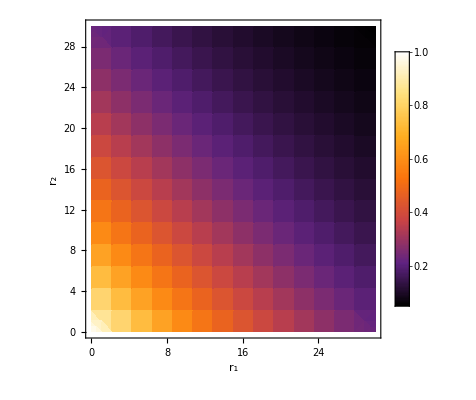

```mathematica
DensityPlot[Exp[(-r1-r2)*.1/2],{r1,0,30},{r2,0 ,30},ColorFunction->"SunsetColors",FrameLabel->{ToExpression["r_1",TeXForm,HoldForm],ToExpression["r_2",TeXForm,HoldForm]},(*Add some labels*)LabelStyle->{Black,15},(*Change label style*)PlotLegends->True (*Add a legend*)]
```

```mathematica
Manipulate[ContourPlot[Exp[(-x-y)],{x,0,1},{y,0,1},ColorFunction->"DarkRainbow"],{z,0,1}]
```